```mathematica
ClearAll["Global`*"]
```

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

D:\simulation\TEST\cdw_mathematica_9x9

```mathematica
Top
```

```mathematica
1.Define Band structure parameters& some useful constants
2. Define tight-binding model dispersion
3. Finding Fermi surface with grid search algorithm
4. Calculate ADMR
5. Process and plot data
6. General dispersion (test)
```

```mathematica
$HistoryLength=0;
```

# Define Band structure parameters & some useful constants

```mathematica
c=13.2; 
a =5.3/Sqrt[2];
b=5.3/Sqrt[2];
ℏ=1.05*10^-34;
e=1.6*10^-19;
m0=9.1*10^-31;
kB=1.38*10^-23;
jtoev=6.242*10^18; (*conversion constant from juole to eV*)
ty= 1.6*10^-22 * 1/(9.1*10^-31) 1/(10^-10)^2 10^-24;



(*v [f_]:=(9.1*10^-31)10^-20/(10^-12)*1/ℏ{D[f,kx],D[f,ky],D[f,kz]};
kf[F_]:=Sqrt[(F 2Pi (e/(1.6*10^-19))/(ℏ/(9.1*10^-31)*10^20) (1/10^-12))/Pi];*)
```

```mathematica
return to top
```

# Define tight-binding model

```mathematica
t=190*ty;
tp=-0.16*t;
tpp=0.07*t;
tz=0.035*t;
μ = 0.685*t;
ξ[kx_?NumericQ,ky_?NumericQ,mu_?NumericQ]:=-2t(Cos[kx a]+Cos[ky b])-2tp(Cos[kx a+ky b]+Cos[kx a- ky b])-2tpp(Cos[2kx a]+Cos[2ky b])+mu;
ξz[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=-2 tz*Cos[kz c/2](Cos [kx a ]-Cos[ky b])^2 Cos[(kx a )/2]Cos[(ky b )/2];


Q=2π/3/a;
(*here it could be functions of kx and ky like for dwave density waves*)
B=0(*-0.07*t*);
AA=0.1*t;

(*here it could be functions of kx and ky like for dwave density waves*)
tyQ[kx_?NumericQ,ky_?NumericQ]:=AA-B*(Cos[kx a]-Cos[ky b]);
txQ[kx_?NumericQ,ky_?NumericQ]:=AA-B*(Cos[kx a]-Cos[ky b] );
tsyQ[kx_?NumericQ,ky_?NumericQ]:=AA-B*(Cos[kx a]-Cos[ky b]);
tsxQ[kx_?NumericQ,ky_?NumericQ]:=AA-B*(Cos[kx a]-Cos[ky b]);

BDW2d[kx_?NumericQ,ky_?NumericQ,mu_?NumericQ]:=({{ξ[kx,ky,mu], -tyQ[kx,ky+Q/2], -tyQ[kx,ky-Q/2], -txQ[kx+Q/2,ky], 0, 0, -txQ[kx-Q/2,ky], 0, 0}, {-tyQ[kx,ky+Q/2], ξ[kx,ky+Q,mu], -tyQ[kx,ky-3/2Q], 0, -tsxQ[kx+Q/2,ky+Q], 0, 0, -tsxQ[kx-Q/2,ky+Q], 0}, {-tyQ[kx,ky-Q/2], -tyQ[kx,ky+3/2Q], ξ[kx,ky+2Q,mu], 0, 0, -tsxQ[kx+Q/2,ky-Q], 0, 0, -tsxQ[kx-Q/2,ky-Q]}, {-txQ[kx+Q/2,ky], 0, 0, ξ[kx+Q,ky,mu], -tsyQ[kx+Q,ky+Q/2], -tsyQ[kx+Q,ky-Q/2], -txQ[kx-3/2Q,ky], 0, 0}, {0, -tsxQ[kx+Q/2,ky+Q], 0, -tsyQ[kx+Q,ky+Q/2], ξ[kx+Q,ky+Q,mu], -tsyQ[kx+Q,ky-3/2Q], 0, -tsxQ[kx-3/2Q,ky+Q], 0}, {0, 0, -tsxQ[kx+Q/2,ky-Q], -tsyQ[kx+Q,ky-Q/2], -tsyQ[kx+Q,3/2Q+ky], ξ[kx+Q,ky+2Q,mu], 0, 0, -tsxQ[kx-3/2Q,ky-Q]}, {-txQ[kx-Q/2,ky], 0, 0, -txQ[kx+3/2Q,ky], 0, 0, ξ[kx+2Q,ky,mu], -tsyQ[kx-Q,ky+Q/2], -tsyQ[kx-Q,ky-Q/2]}, {0, -tsxQ[kx-Q/2,ky+Q], 0, 0, -tsxQ[kx+3/2Q,ky+Q], 0, -tsyQ[kx-Q,ky+Q/2], ξ[kx+2Q,ky+Q,mu], -tsyQ[kx-Q,ky-3/2Q]}, {0, 0, -tsxQ[kx-Q/2,ky-Q], 0, 0, -tsxQ[kx+3/2Q,ky-Q], -tsyQ[kx-Q,ky-Q/2], -tsyQ[kx-Q,ky+3/2Q], ξ[kx+2Q,ky+2Q,mu]}});
BDWbands[kx_?NumericQ,ky_?NumericQ,mu_?NumericQ]:=BDWbands[kx,ky,mu]=Sort[Eigenvalues[BDW2d[kx,ky,mu]]];
```

# Calculationg of the doping of the un - reconstruced band

```mathematica
doping=0;
f[kx_?NumericQ,ky_?NumericQ]:=ξ[kx,ky,μ]
area=NIntegrate[Boole[f[kx,ky]>= 0],{kx,-Pi/a,Pi/a},{ky,-Pi/a,Pi/a}];
atotal= (2Pi/a)(2Pi/b);
per = area/atotal
doping=per*2-1
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.57156 and 0.000636844 for the integral and error estimates.

0.559105

0.118211

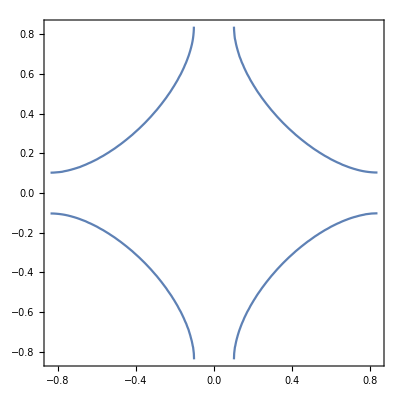

```mathematica
ContourPlot[ξ[x,y,μ](*+ξz[x,y,0]==*)==0,{x,-Pi/a,Pi/a},{y,-Pi/a,Pi/a}]
```

# BDW Spectral weight in the full brillouin zone It is faster to compute the spectral weight than a contour plot

```mathematica
SpectralWeight[x_]:=Blend[{{0,RGBColor[1,1,1]},{0.002,RGBColor[0.866,0.866,0.866]},{0.05,RGBColor[0,0,1,1]},{0.66,RGBColor[1,0.5,0,1]},{1,RGBColor[1,0,0,1]}},x];
```

```mathematica
ClearAll[A]
```

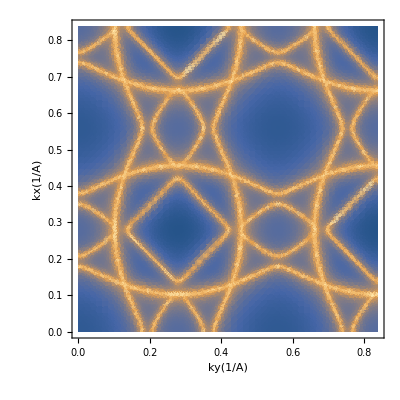

```mathematica
η=0.002*t;
A[kx_, ky_,mu_,ω_]:=Tr[Im[Inverse[((ω-I*η)*IdentityMatrix[9]- BDW2d[kx, ky,mu])]]
]/π;
Show[DensityPlot[Log[A[kx,ky,μ,0]],{ky,0,Pi/a},{kx,0,Pi/a},PlotPoints->50,PlotRange->Full,AspectRatio->1/1(*,ColorFunction->SpectralWeight*),Frame->True,FrameLabel->{{ Text[Style["kx(1/A)",FontSize->24,FontFamily->"Helvetica"]],None},{ Text[Style["ky(1/A)",FontSize->24,FontFamily->"Helvetica"]],None}}]]
```

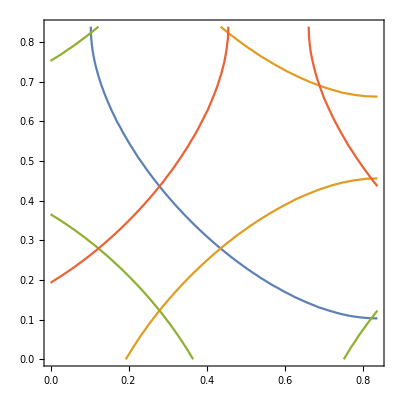

```mathematica
Show[ContourPlot[{ξ[kx,ky,μ]==0,ξ[kx,ky-Q,μ]==0,ξ[kx-Q,ky-Q,μ]==0,ξ[kx-Q,ky,μ]==0},{kx,0,Pi/a},{ky,0,Pi/a}],DensityPlot[A4[kx,ky,μ,0],{ky,0,π/a},{kx,0,π/a},PlotPoints->100,PlotRange->Full,AspectRatio->1/1,ColorFunction->customColor]]
```

```mathematica
return to top
```

```mathematica
Build 2 D interpolated function(test)
```

Some ideas of general dispersion :
1. I think it is definitely possible to do the ADMR calculation with general dispersion. The difficulty would be to isolation a single piece of Fermi surface and have a uniform grid or do some clever symmetry/linear transformation of the grid or something...
2. The current notebook only consider a general in-plane dispersion. I think for highly 3D band it is also possible, but it need a bit change of the code. 
procedure(the current notebook only deal with one parameter, which is the relaxation time):
1. load the dispersion computed on a uniform 2D grid , start from here.

```mathematica
Test dispersion grid
```

```mathematica
dist=1.0*0.595
FSindex=4
UpperBx ={0.37*a,.663*a,1.58,(1.04+dist)};
LowerBx ={0.2*a,0.45*a,0.5,(1.04-dist)};
UpperBy ={1.14* 0.09*a,1.58,0.663*a,(1.04+dist)};
LowerBy ={-1.14* 0.09*a,0.5,0.45*a,(1.04-dist)};
differy = UpperBy - LowerBy 
differx = UpperBx - LowerBx
```

```mathematica
numb =100
EngInt[kx_?NumericQ,ky_?NumericQ]:=BDWbands[kx, ky,μ][[4]];  (*interpolation function CDW band *)
plot1=Flatten[Table[{kx,ky,EngInt[kx,ky]},{kx,(LowerBx[[FSindex]]-3*differx[[FSindex]]/numb)/a,(UpperBx[[FSindex]]+3*differx[[FSindex]]/numb)/a,differx[[FSindex]]/numb/a},{ky,(LowerBy[[FSindex]]-3*differx[[FSindex]]/numb)/a,(UpperBy[[FSindex]]+3*differx[[FSindex]]/numb)/a,differy[[FSindex]]/numb/a}],1];(*compute 2D interpolation grid*)
(*refineselect = Select[plot1,#[[3]]>-2*tz&&#[[3]]<2*tz &];*)
test =  Interpolation[plot1,InterpolationOrder->2];
func[x_,y_] := Piecewise[{{test[x,y],x>0 &&y>0},{test[x,-y],x>0 && y < 0},{test[-x,-y],x<0 && y < 0},{test[-x,y],x<0 && y > 0}}]
(*V[kx_,ky_,kz_]:= (9.1*10^-31)10^-20/(10^-12)*1/ℏ*{(eng[kx+h,ky,kz]-eng[kx,ky,kz])/h,(eng[kx,ky+h,kz]-eng[kx,ky,kz])/h,(eng[kx,ky,kz+h]-eng[kx,ky,kz])/h};*)
```

100

```mathematica
Show[ListPointPlot3D[plot1]]
```

-Graphics3D-

# Export grid (for testing general band structure )

```mathematica
Export["grid.dat",plot1,"Table"]
```

grid.dat

# For general band structure import the dispersion (E(kx,ky) on a regular grid)

```mathematica
testdat = Import["grid.dat","Table"];(*load the file here*)
test =  Interpolation[testdat,InterpolationOrder->2];
func[x_,y_] := Piecewise[{{test[x,y],x>0 &&y>0},{test[x,-y],x>0 && y < 0},{test[-x,-y],x<0 && y < 0},{test[-x,y],x<0 && y > 0}}] (*build the full fermi surface given the symmetry of the system*)
eng[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=func[kx,ky]+ξz[kx,ky,kz];(*3D dispersion*)
```

```mathematica
Show[Plot3D[eng[x,y,0],{x,0.122,0.439},{y,0.436,0.119},PlotRange->All](*,ListPointPlot3D[plot1]*),Plot3D[{0},{x,0.122,0.439},{y,0.436,0.119},PlotStyle->Blue]]
```

-Graphics3D-

```mathematica
return to top
```

# Finding Fermi surface with grid search algorithm (modified marching square?)

Algorithm description :
1. Compute the E(kx,ky) on a coarse grid and select the grids where the FS crosses some of its’s edges.
2. Define a finer grid in each of the selected grid and repeat the process refineNum of times
3. Process the final grid and find the approximate points where the FS crosses
4. pre-defined a center of the closed FS (centerx,centery)
5. Compute the Arctan with respect to the center (centerx,centery) for all the points from step 3
6. Sort the points by their Arctan, and compute accumulative sum of the sorted list
7. compute a uniform grid of the FS

Potential problems:
1. need to identify a area where there are only one piece of FS. With the current version, this need to be done by hand
2. if more than one piece of FS is in the area, extra logic need to be used to selected out a particular piece before running step 5 -7
3. need to identify the center of the FS. With the current version, this also need to be done by hand
4.the current version assume 4fold rotational symmetry and the CDW FS is only computed in the range {kx,0, Pi/a}{ky,0,Pi/a} and rotated to get the other 3 FS pieces

```mathematica
Parameters for the algorithm
```

```mathematica
dist=1.05*0.58 (*starting from the center of the cdw diamond FS, the width of the*) 
UpperBx ={0.37*a,.663*a,1.58,(1.04+dist)}; (*a list of upper bound of kx*)
LowerBx ={0.2*a,0.45*a,0.5,(1.04-dist)}; (*a list of lower bound of kx*)
UpperBy ={1.14* 0.09*a,1.58,0.663*a,(1.04+dist)};(*a list of upper bound of ky*)
LowerBy ={-1.14* 0.09*a,0.5,0.45*a,(1.04-dist)};(*a list of lower bound of ky*)
centerx={Pi/3,Pi 2/3.,0.28*a,Pi/3};
centery={0,0.28*a,Pi 2/3.,Pi/3}
differy = UpperBy - LowerBy 
differx = UpperBx - LowerBx 
numb =20;(*the size of the initial coarse grid*)
gridnum=200;(*the final size of each inplane FS*)
subnum = 4;(*the size of the finder grid*)
h = 10^-8;(*the step for finite difference computation*)
cdev=6;(*the number kz slice*)
refineNum =3;(*the number of times step 3 is repeated*)
eng[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=func[kx,ky]+ξz[kx,ky,kz];(*3D dispersion*)
```

0.609

{0,1.04935,2.0944,π/3}

{0.769021,1.08,0.798253,1.218}

{0.637103,0.798253,1.08,1.218}

```mathematica
Algoritm
```

```mathematica
start={};
circ={};
Block[{plot1,plotTot,ConOri,Con,plot1sub,plotTotsub,Bsort,diff,interpoY,interpoX,funcX,funcY,rowpoint, colpoint},
Do[
(*Step 1: Initial mesh*)
zrang ={0}(*Range[-2.*Pi/c+4.*Pi/c/cdev/2,2.*Pi/c,4.*Pi/c/cdev]*);

plot1=Table[Table[{kx,ky, If[eng[kx,ky,kz]>0,1,0]},{kx,(LowerBx[[FSindex]])/a,(UpperBx[[FSindex]])/a,differx[[FSindex]]/numb/a},{ky,LowerBy[[FSindex]]/a,UpperBy[[FSindex]]/a,differy[[FSindex]]/numb/a}],{kz,zrang}];
plotTot =Table[Flatten[Table[ Table[{1/4*(plot1[[k,j,i,1]]+plot1[[k,j+1,i,1]]+plot1[[k,j,i+1,1]]+plot1[[k,j+1,i+1,1]]),1/4*(plot1[[k,j,i,2]]+plot1[[k,j+1,i,2]]+plot1[[k,j,i+1,2]]+plot1[[k,j+1,i+1,2]]),If[(plot1[[k,j,i,3]]+plot1[[k,j+1,i,3]]+plot1[[k,j,i+1,3]]+plot1[[k,j+1,i+1,3]])<3.5,If[(plot1[[k,j,i,3]]+plot1[[k,j+1,i,3]]+plot1[[k,j,i+1,3]]+plot1[[k,j+1,i+1,3]])>0.5,1],0]},{i,1,Length[plot1[[k,j]]]-1}],{j,1,Length[plot1[[k]]]-1}],1],{k,1,Length[zrang]}];
ConOri = Table[Transpose[Transpose[Select[plotTot[[j]],If[FSindex==4,(#[[3]]==1&&Sqrt[(#[[1]]-1.05/a*1)^2+(#[[2]]-1.05/a*1)^2]<0.96dist/a),(#[[3]]==1)]&]][[{1,2}]]],{j,1,Length[zrang]}];
Con=ConOri;
cellsizeY=differy/numb/a;
cellsizeX=differx/numb/a;


(*Step 2: Refined mesh*)

Do[

plot1sub=Table[Table[Table[Table[{kx,ky, If[eng[kx,ky,zrang[[j]]]>0,1,0]},{kx,(Con[[j,i,1]]-cellsizeX[[FSindex]]/2),(Con[[j,i,1]]+cellsizeX[[FSindex]]/2),cellsizeX[[FSindex]]/subnum}],{ky,(Con[[j,i,2]]-cellsizeY[[FSindex]]/2),(Con[[j,i,2]]+cellsizeY[[FSindex]]/2),cellsizeY[[FSindex]]/subnum}],{i,1,Length[Con[[j]]]}],{j,1,Length[zrang]}];
plotTotsub =Table[ Flatten[Table[Table[Table[{1/4*(plot1sub[[kz,pi,j,i,1]]+plot1sub[[kz,pi,j+1,i,1]]+plot1sub[[kz,pi,j,i+1,1]]+plot1sub[[kz,pi,j+1,i+1,1]]),1/4*(plot1sub[[kz,pi,j,i,2]]+plot1sub[[kz,pi,j+1,i,2]]+plot1sub[[kz,pi,j,i+1,2]]+plot1sub[[kz,pi,j+1,i+1,2]]),If[(plot1sub[[kz,pi,j,i,3]]+plot1sub[[kz,pi,j+1,i,3]]+plot1sub[[kz,pi,j,i+1,3]]+plot1sub[[kz,pi,j+1,i+1,3]])<3.5,If[(plot1sub[[kz,pi,j,i,3]]+plot1sub[[kz,pi,j+1,i,3]]+plot1sub[[kz,pi,j,i+1,3]]+plot1sub[[kz,pi,j+1,i+1,3]])>0.5,1],0]},{i,1,Length[plot1sub[[kz,pi,j]]]-1}],{j,1,Length[plot1sub[[kz,pi]]]-1}],{pi,1,Length[plot1sub[[kz]]]}],2],{kz,1,Length[zrang]}];

Con = Table[Transpose[Transpose[Select[plotTotsub[[j]],(#[[3]]==1)&]][[{1,2}]]]
,{j,1,Length[zrang]}];
cellsizeY[[FSindex]]=cellsizeY[[FSindex]]/subnum;
cellsizeX[[FSindex]]=cellsizeX[[FSindex]]/subnum;
Print[Dimensions[Con[[1]]]]
,refineNum];
(*Step 3: process final grid*)
rowpoint= Table[Flatten[Table[Table[Table[{1/2*(plot1sub[[kz,pi,j,i,1]]+plot1sub[[kz,pi,j+1,i,1]]),0.5*(plot1sub[[kz,pi,j,i,2]]+plot1sub[[kz,pi,j+1,i,2]]),If[Xor[plot1sub[[kz,pi,j,i,3]]>0.5,plot1sub[[kz,pi,j+1,i,3]]>0.5],1,0]},{i,1,Length[plot1sub[[kz,pi,j]]]}],{j,1,Length[plot1sub[[kz,pi]]]-1}],{pi,1,Length[plot1sub[[kz]]]}],2],{kz,1,Length[zrang]}];
colpoint= Table[Flatten[Table[Table[Table[{1/2*(plot1sub[[kz,pi,j,i,1]]+plot1sub[[kz,pi,j,i+1,1]]),0.5*(plot1sub[[kz,pi,j,i,2]]+plot1sub[[kz,pi,j,i+1,2]]),If[Xor[plot1sub[[kz,pi,j,i,3]]>0.5,plot1sub[[kz,pi,j,i+1,3]]>0.5],1,0]},{i,1,Length[plot1sub[[kz,pi,j]]]-1}],{j,1,Length[plot1sub[[kz,pi]]]}],{pi,1,Length[plot1sub[[kz]]]}],2],{kz,1,Length[zrang]}];
Con= Table[Transpose[Transpose[Join[Select[rowpoint[[j]],(#[[3]]==1)&],Select[colpoint[[j]],(#[[3]]==1)&]]][[{1,2}]]]
,{j,1,Length[zrang]}];

(*Step 5: compute arctan and sort*)
Bsort =  Table[Transpose[Transpose[SortBy[ Table[{Con[[j,i,1]],Con[[j,i,2]],ArcTan[Con[[j,i,1]]-centerx[[FSindex]]/a,Con[[j,i,2]]-centery[[FSindex]]/a]},{i,1,Length[Con[[j]]]}],Last]][[{1,2}]]],{j,1,Length[zrang]}];(*Step 6: compute accumulative sum and find the uniform FS grid*)
diff =Table[Join[{0}, Accumulate[Table[Sqrt[(Bsort[[j,i,1]]-Bsort[[j,i+1,1]])^2+(Bsort[[j,i,2]]-Bsort[[j,i+1,2]])^2],{i,1,Length[Bsort[[j]]]-1}]]],{j,1,Length[zrang]}];
interpoX= Table[Transpose[{SetPrecision[diff[[j]],10],Bsort[[j,All,1]]}],{j,1,Length[zrang]}];
interpoY=  Table[Transpose[{SetPrecision[diff[[j]],10],Bsort[[j,All,2]]}],{j,1,Length[zrang]}];
funcX = Table[Interpolation[DeleteDuplicatesBy[interpoX[[j]],First],InterpolationOrder->1],{j,1,Length[zrang]}];
funcY = Table[Interpolation[DeleteDuplicatesBy[interpoY[[j]],First],InterpolationOrder->1],{j,1,Length[zrang]}];
start =Join[start,Flatten[{Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1],Dot[#,{{Cos[Pi/2],-Sin[Pi/2],0},{Sin[Pi/2],Cos[Pi/2],0},{0,0,1}}]&/@Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1],Dot[#,{{Cos[Pi],-Sin[Pi],0},{Sin[Pi],Cos[Pi],0},{0,0,1}}]&/@Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1],Dot[#,{{Cos[3 Pi/2],-Sin[3Pi/2],0},{Sin[3Pi/2],Cos[3Pi/2],0},{0,0,1}}]&/@Flatten[Table[Drop[Table[{funcX[[j]][x],funcY[[j]][x],zrang[[j]]},{x,0,diff[[j,Length[diff[[j]]]]],diff[[j,Length[diff[[j]]]]]/gridnum}],-1],{j,1,Length[zrang]}],1]},1]];
circ=Join[circ,Flatten[Table[Table[Table[diff[[j,Length[diff[[j]]]]]/gridnum,{i,1,gridnum(*phispecial*)}],{j,1,Length[zrang]}],{4}],2]];,{FSindex,{4}(*Length[UpperBx]*)}];
ClearSystemCache[];]
start01=start;
circ01=circ;
```

{280,2}

{1120,2}

{4480,2}

```mathematica
ListPointPlot3D[start01]
```

-Graphics3D-

```mathematica
return to top
```

```mathematica
Calculate ADMR
```

```mathematica
tdevs=800;(*number of time step for differential equation*)
θdevs=4; (*number of θ angle*)
θmax=100; (*maximum θ angle*)
θmin=0; (*minimum θ angle*)
thetas =(*{80.,100.}*Pi/180*) Table[θ,{θ,θmin*Pi/180,θmax*Pi/180.,(θmax-θmin)*Pi/180./θdevs}]; 
phis = {0.*Pi/180(*,15.*Pi/180,30.*Pi/180,45.*Pi/180*)}; (*phi angle list*)
param=Flatten[Table[{the,phi},{the,thetas},{phi,phis}],1] (*parameter list*)
hopping={{0.1}};(*tau*)
```

{{0.,0.},{0.436332,0.},{0.872665,0.},{1.309,0.},{1.74533,0.}}

```mathematica
Brange=(*Range[41,45,1]*){45}; (*magnetic field strength*)
tnum =8; (**)

numbTimes=1;
numGrid01=Length[start01];


(*velocityz01=velocity01[[3]];*)
 cond01= Table[Table[{0,0,0},{Length[thetas]}],{Length[phis]}];

(*start01= Drop[Import["FS_kx_ky_kz.dat","Table"],1];
 *)
Bfield=45*1.6*10^-19 * 10^-12/(9.1*10^-31);
(*efun=Compile[{{kx,_Real},{ky,_Real},{kz,_Real}},inplanFermi[kx,ky]+ξz[kx,ky,kz]];*)
efun01[kx_?NumericQ,ky_?NumericQ,kz_?NumericQ]:=func[kx,ky]+ξz[kx,ky,kz];


h=10^-8;
velocity01=(9.1*10^-31)10^-20/(10^-12)*1/ℏ*1/h({efun01[kx+h,ky,kz]-efun01[kx,ky,kz],efun01[kx,ky+h,kz]-efun01[kx,ky,kz],efun01[kx,ky,kz+h]-efun01[kx,ky,kz]});
velZ[kx_,ky_,kz_]=velocity01[[3]];
Dx01=(efun01[kx+h,ky,kz]-efun01[kx,ky,kz])/h;
Dy01=(efun01[kx,ky+h,kz]-efun01[kx,ky,kz])/h;
Dz01=(efun01[kx,ky,kz+h]-efun01[kx,ky,kz])/h;
```

```mathematica
cond01=Table[{0,0,0},Length[param]]
AbsoluteTiming[

ParallelDo[
Module[{(*kx1,ky1,kz1,*)p1,gridIndex,B = {0,0,1},state01,state11,state21,solution01=Table[Null,{Length[start01]}],(*Dx01,Dy01,Dz01,*)τ=hopping[[numbTimes,1]],
τt=tnum*hopping[[numbTimes,1]],τs=tnum*hopping[[numbTimes,1]]/tdevs,times=Range[0,tnum*hopping[[numbTimes,1]],tnum*hopping[[numbTimes,1]]/tdevs],V01,Exps,taus,tauSum,result},


(*times=Range[0,tnum*hopping[[numbTimes,1]],tnum*hopping[[numbTimes,1]]/tdevs];
solution01=Table[Null,{Length[start01]}];*)
B = {Bfield*Sin[param[[index,1]]]Cos[param[[index,2]]],Bfield*Sin[param[[index,1]]]Sin[param[[index,2]]],Bfield*Cos[param[[index,1]]]};

cond01[[index]]={param[[index,2]]*180./Pi,param[[index,1]]*180./Pi,0};


state01=First@NDSolve`ProcessEquations[{(11538.5)kx'[tvar] == -(1)Cross[velocity01/.kx->kx[tvar]/.ky->ky[tvar]/.kz->kz[tvar],B][[1]],(11538.5)ky'[tvar] == -(1)Cross[velocity01/.kx->kx[tvar]/.ky->ky[tvar]/.kz->kz[tvar],B][[2]],(11538.5)kz'[tvar] == -(1)Cross[velocity01/.kx->kx[tvar]/.ky->ky[tvar]/.kz->kz[tvar],B][[3]],kx[0] ==  start01[[1,1]],ky[0] ==  start01[[1,2]],kz[0] ==  start01[[1,3]]},{kx,ky,kz},tvar];

NDSolve`Iterate[state01,hopping[[numbTimes,1]]*(tnum+1)];
 solution01[[1]]=NDSolve`ProcessSolutions[state01];

For[p1=2,p1≤ Length[start01](*numGrid01*),p1++,
 state01=First@NDSolve`Reinitialize[state01,{kx[0] ==  start01[[p1,1]],ky[0] ==  start01[[p1,2]],kz[0] ==  start01[[p1,3]]}];
NDSolve`Iterate[state01,hopping[[numbTimes,1]]*(tnum+1)];
solution01[[p1]]=NDSolve`ProcessSolutions[state01];
];

Print[index];

V01=Table[velZ[solution01[[i,1,2]][#],solution01[[i,2,2]][#],solution01[[i,3,2]][#]]&/@times,{i,1,Length[start01]}];
Exps=Exp[-(times)/hopping[[numbTimes,1]]]*τs*10^-12;
cond01[[index,3]] = cond01[[index,3]]+Total[Table[((1/Sqrt[(Dx01/.kx->solution01[[i,1,2]][0]/.ky->solution01[[i,2,2]][0]/.kz->solution01[[i,3,2]][0])^2 +(Dy01/.kx->solution01[[i,1,2]][0]/.ky->solution01[[i,2,2]][0]/.kz->solution01[[i,3,2]][0])^2+(Dz01/.kx->solution01[[i,1,2]][0]/.ky->solution01[[i,2,2]][0]/.kz->solution01[[i,3,2]][0])^2])*
circ01[[i]]*4*Pi/c/cdev*(velocity01[[3]]/.kx->solution01[[i,1,2]][0]/.ky->solution01[[i,2,2]][0]/.kz
->solution01[[i,3,2]][0] )*
(Total[V01[[i]]*Exps])),{i,1,numGrid01,1}]];
str01=StringJoin[dir,"\\Calculations\\cdw_param",ToString[index],".dat"];
Export[str01,{cond01[[index]]}];
Remove[state01,state11,state21,solution01,times,V01,Exps,taus,tauSum,result];
ClearSystemCache[];]
,{index,Length[param]}]]
str01=Table[StringJoin[dir,"\\Calculations\\cdw_param",ToString[index],".dat"],{index,1,Length[param]}];
cond01 =Table[Import[#]&/@str01[[i]],{i,Length[str01]}];
cond01exp=Flatten[Import[#]&/@Flatten[str01,1],1];
Export[StringJoin[dir,"\\cdw_elect_tau_0p054.dat"],cond01exp,"Table"];
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

3

1

4

5

2

{9760.94,Null}

```mathematica
return to top
```

# Process and plot data

```mathematica
cond01dat=SortBy[Import[StringJoin[dir,"\\cdw_elect_tau_0p054_n1.dat"],"Table"],First];
conphi = DeleteDuplicates[cond01dat[[All,1]]]
coplot = Table[Select[cond01dat,#[[1]]==conphi[[i]]&][[All,{2,3}]],{i,1,Length[conphi]}]
conInt = Interpolation[#]&/@coplot;
confinal =Table[ Table[{th,conInt[[i]][0]/conInt[[i]][th]},{th,0,100,2}],{i,1,Length[conInt]}];
```

{0.}

{{{0.,1.03727×10^-18},{12.5,1.02876×10^-18},{25.,1.00272×10^-18},{37.5,9.58754×10^-19},{50.,9.02232×10^-19},{62.5,8.55459×10^-19},{75.,8.44085×10^-19},{87.5,8.24096×10^-19},{100.,8.41214×10^-19}}}

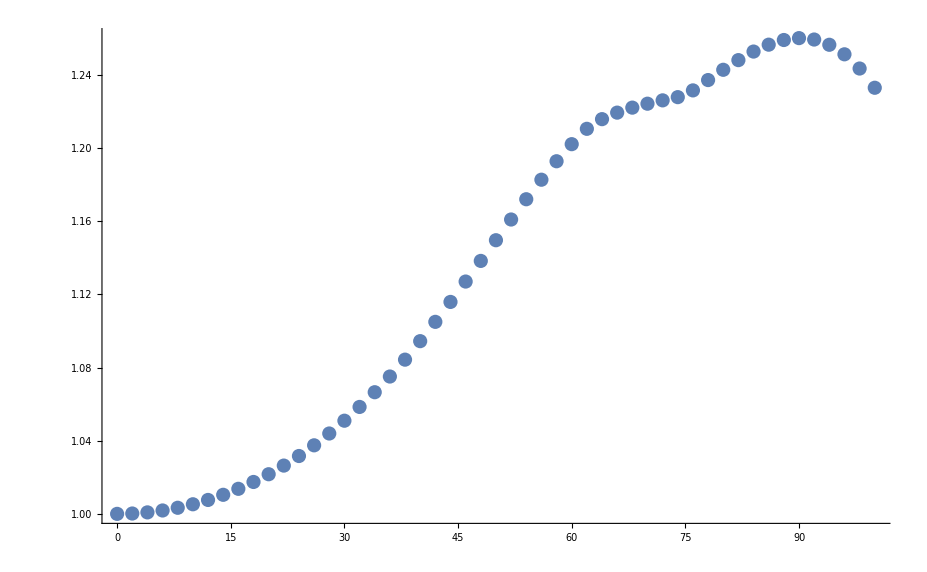

```mathematica
{ListPlot[confinal]}
```

```mathematica
return to top
```